In this notebook, we aim to find the mismatch in evolutionary rate expected, given our within host data and a given decline in transmission fitness as the number of mutations accumulates.

File Directories

```mathematica
indivSequencesDir="pathname_here";(*directory with the individual level sequences*)
```

```mathematica
mismatchDir="pathname_here";(*directory where the files showing the distance from ancestor will be saved*)
```

User Defined Functions

```mathematica
Needs["ErrorBarPlots`"]
```

### SNP[seq1_, seq2_] The position of sites where sequence 1 ≠ sequence 2 and where there isn’t an “-“

```mathematica
SNP[seq1_,seq2_]:=Position[MapThread[#1≠#2&&#1≠"-"&&#2≠"-"&&#1≠"N"&&#2≠"N"&,{seq1,seq2}],True]//Flatten
```

### CodonPos[pos_] Gives the nucleotides positions for the complete codon given a single nucleotide position

```mathematica
CodonPos[pos_]:=Which[
Mod[pos,3]==1,{pos,pos+1,pos+2},
Mod[pos,3]==2,{pos-1,pos,pos+1},
Mod[pos,3]==0,{pos-2,pos-1,pos}]
```

### CodonToAA[codon_] Given a codon (as a single string of 3 nucleotides) this gives the corresponding amino acid

Given a codon (as a single string of 3 nucleotides) this gives the corresponding amino acid

```mathematica
CodonToAA[codon_]:=Block[{RNACodonTable},
RNACodonTable={
{"TTT","F"},
{"TTC","F"},
{"TTA","L"},
{"TTG","L"},
{"CTT","L"},
{"CTC","L"},
{"CTA","L"},
{"CTG","L"},
{"ATT","I"},
{"ATC","I"},
{"ATA","I"},
{"ATG","M"},
{"GTT","V"},
{"GTC","V"},
{"GTA","V"},
{"GTG","V"},
{"TCT","S"},
{"TCC","S"},
{"TCA","S"},
{"TCG","S"},
{"CCT","P"},
{"CCC","P"},
{"CCA","P"},
{"CCG","P"},
{"ACT","T"},
{"ACC","T"},
{"ACA","T"},
{"ACG","T"},
{"GCT","A"},
{"GCC","A"},
{"GCA","A"},
{"GCG","A"},
{"TAT","Y"},
{"TAC","Y"},
{"TAA","Stop"},
{"TAG","Stop"},
{"CAT","H"},
{"CAC","H"},
{"CAA","Q"},
{"CAG","Q"},
{"AAT","N"},
{"AAC","N"},
{"AAA","K"},
{"AAG","K"},
{"GAT","D"},
{"GAC","D"},
{"GAA","E"},
{"GAG","E"},
{"TGT","C"},
{"TGC","C"},
{"TGA","Stop"},
{"TGG","W"},
{"CGT","R"},
{"CGC","R"},
{"CGA","R"},
{"CGG","R"},
{"AGT","S"},
{"AGC","S"},
{"AGA","R"},
{"AGG","R"},
{"GGT","G"},
{"GGC","G"},
{"GGA","G"},
{"GGG","G"}};
Select[RNACodonTable,#[[1]]==codon&][[1,2]]
];
```

### SeqDat[ans_,seq_,name_] Given a sequence, this give the list {time point, number of copies of sequence, number of mutations, synonymous mutations, and nonsynonymous mutations} from the nearests ancestral consensus sequence at the first timepoint

```mathematica
SeqDat[ans_,seq_,name_]:=Block[{snps,nMuts,ansIndex,snpCodon,ansAA,seqAA,nSynon},
Off[Part::partw];
Off[StringJoin::string];

snps=Map[SNP[#,seq]&,ans];;(*the positions where each ancestral consensus sequence ≠ seqeunce*)
nMuts=Min[Map[Length,snps]];(*the number of differences between seqeunce and the closest ancestor*)
ansIndex=Position[Map[Length,snps],nMuts][[1,1]];(*the index of the ancestral sequence to which the sequence is the closest.  If equal distance to more than one ancestral sequence it will give the lowest index*)
snpCodon=CodonPos/@snps[[ansIndex]];(*the codon triplets where there is a difference*)
ansAA=CodonToAA/@StringJoin/@Map[ans[[ansIndex]][[#]]&,snpCodon];(*the AA in the consensus sequence associated with each SNP*)
seqAA=CodonToAA/@StringJoin/@Map[seq[[#]]&,snpCodon];(*the AA associated with difference in the sequence*)
nSynon=Count[MapThread[#1==#2&,{ansAA,seqAA}],True];(*the number of synonymous mutations*)

On[Part::partw];
On[StringJoin::string];

{ToExpression[StringSplit[name,"_"][[{5,3}]]],nMuts,nSynon,nMuts-nSynon}//Flatten]
```

### DistanceFromAncestor[patient_,region_] Returns a table giving {the time point, number of copies, number all muts, number synon muts, number nonsynon muts} from the nearest ancestor for all sequences, for a given patient-region combination

```mathematica
DistanceFromAncestor[patient_,region_]:=Block[{ansFilename,ancestors,ansTab,seqData,names,sequences,seqTab,output},
SetDirectory[];SetDirectory[indivSequencesDir];
ansFilename=patient<>"_"<>region<>"_firsttimepoint_consensus.fasta";
ancestors=Import[ansFilename,{"FASTA"}];(*these are the patient ancestral sequences as calculated from BAPS*)
ancestors=StringReplace[ancestors," "->""];(*as above, but with any spaces removed*)
ansTab=Table[StringSplit[ancestors[[i]],""],{i,1,Length[ancestors]}];(*as above, but each sequence represented as a list*)
seqData=Import[patient<>"_"<>region<>".fasta",{"FASTA","Data"}];(*import all the seqeunces for each individual patient*)
names=seqData[[1]];(*the seqeunce names for each individual sequence*)
sequences=StringReplace[seqData[[2]]," "->""];(*the individual sequences with spaces removed*)
seqTab=Table[StringSplit[sequences[[i]],""],{i,1,Length[sequences]}];(*as above, but each sequence represented as a list*)
output=Table[SeqDat[ansTab,seqTab[[ii]],names[[ii]]],{ii,1,Length[names]}];(*for each seqeunce this gives the time point, number of copies, number muts, number synon muts, number nonsynon muts from the closest ancestor*)

PrependTo[output,{"timestamp","copies","all","synon","nonsynon"}];
output]
```

### Transmitted[patient_, region_, alpha_] returns the number of transmitted mutations for all, synonymous and nonsynonymous mutations from the ancestral sequences, assuming fitness depends on number of all mutations for each sequence. When alpha = 0, there is no selection at transmission

```mathematica
(*this gives transmitted mutations assuming fitness depends on number of all mutations for each sequence*)
Transmitted[patient_,region_,alpha_]:=Block[{distanceTab,stamps,nMutMax,fitness,fitnessTab,sumTrans,totTrans,freqTrans,meanTrans

},

SetDirectory[];SetDirectory[mismatchDir];
distanceTab=Import[patient<>"_"<>region<>"_distance_from_ancestor.csv"][[2;;]];(*this imports a table where each row represents a sequence and each column gives the time stamp, number of copies of that sequence, total number of mutations, number of synonymous mutations, and number of nonsynonymous mutations*)

stamps=Sort[DeleteDuplicates[distanceTab[[;;,1]]],#2>#1&];(*gives a list of all of the sampled timepoints*)

nMutMax=Max[distanceTab[[;;,3]]];(*the maximum number of mutations for this patient*)

fitness=Exp[-alpha distanceTab[[;;,3]]];(*for each sequence, this gives its fitness*)
fitnessTab=Join[distanceTab//Transpose,{distanceTab[[;;,2]]fitness}]//Transpose;(*this adds an extra column to distanceTab giving the adjusted number of sequences based on the fitness of that sequence*)

sumTrans=Table[Total[fitnessTab[[Intersection[Position[fitnessTab[[;;,1]],stamps[[tt]]],Position[fitnessTab[[;;,ss]],nn]]//Flatten]][[;;,6]]],{tt,Length[stamps]},{nn,0,nMutMax},{ss,3,5}]//N;(*an nstamp x nMutMax+1 x 3 table giving for each timestamp the ADJUSTED number of sequences with 0,.., nmuttotal mutations for all mutations, synonmymous and nonsynonymous*)


totTrans=Total[sumTrans,{2}];(*gives the total number of sequences (all, synon, nonsynon) for each timepoint*)
freqTrans=sumTrans/Total[sumTrans,{2}][[;;,1]];(*like sumwithin by frequencies*)
meanTrans=Table[Total[freqTrans[[ii]]Range[0,nMutMax],1],{ii,Length[stamps]}]//N;(*gives the mean number of mutations for each timepoint*)

Join[Table[{patient,region,stamps[[ss]],alpha},{ss,Length[stamps]}]//Transpose,meanTrans//Transpose]//Transpose (*gives and nstamp x 7 matrix, where each columb gives the patient, region, time stamp, alpha, mean number of transmitted all, S and NS mutations*)
]
```

### TransmitTab[patients_, regions_, alphas_] For a list of patients, gene regions and alphas, this returns a table where each column gives {patient, region, timestamp, alpha, mean_mutatations_transmitted, mean_Smutatations_transmitted, mean_NSmutatations_transmitted}. alpha=0 corresponds to no selection at transmission, and therefore also reflects the mean number of mutations in an individual before transmission.

```mathematica
TransmitTab[patients_,regions_,alphas_]:=
TransmitTab[patients,regions,alphas]=Block[{tab},
tab={{"patient","region","time","alpha","mean_transmitted","mean_S_transmitted","mean_NS_transmitted"}};
For[pp=1,pp≤Length[patients],pp++,
For[rr=1,rr≤2,rr++,
For[ss=1,ss≤4,ss++,
tab=Join[tab,Transmitted[patients[[pp]],regions[[rr]],alphas[[ss]]]]]]];
tab]
```

### Bootstrap[list_] Performs one bootstrap on a list

```mathematica
Bootstrap[list_]:=list[[RandomChoice[Range[Length[list]],Length[list]]]]
```

### MismatchStats[patients_, region_, alpha_, minDate_, maxDate_, nBootstraps_] Given a gene region, alpha, and a time interval, this finds the expected mismatch if transmission occurs once per patients during each sampling timepoint, for all, S and NS mutations. Also returned are the error bars associated with nBootstraps over the patient data. We assume that fitness at transmission is determined by the total number of mutations on the genome.

```mathematica
MismatchStats[patients_,region_,alpha_,minDate_,maxDate_,nBootstraps_]:=
MismatchStats[patients,region,alpha,minDate,maxDate,nBootstraps]=Block[{regions,tab,mutTab,pos0,posα,temp,totMutTab,mismatch,bootMismatchTab,bootTotMutTab,outstats},
regions={"gag","gp41"};
tab=TransmitTab[patients,{"gag","gp41"},{0,1,2,3}];(*create a transmission table, where each column gives {patient, region, timestamp, alpha, mean_mutations_transmitted, mean_Smutations_transmitted, meanNSmutations_transmitted}. alpha=0 corresponds to the case of selection at transmission, and therefore reflects the mean number of mutations in an individual before transmission*)

mutTab={};(*for the given timeinterval, this will create a table where each row represents a patient, and each column gives mean_mutations_before_transmission, mean_Smutations_before_transmission, mean_NSmutations_before_transmission, mean_mutations_after_transmission, mean_Smutations_after_transmission, mean_NSmutations_after_transmission.  If there is more than one sampling timepoint, the mean in taken. If there are no timepoints, a row of zeros is returned*)

For[pp=1,pp≤Length[patients],pp++,
pos0=Intersection[Position[tab[[;;,1]],patients[[pp]]],Position[tab[[;;,2]],region],Position[tab[[;;,4]],0],Position[tab[[;;,3]],n_/;minDate≤n≤maxDate]]//Flatten;
posα=Intersection[Position[tab[[;;,1]],patients[[pp]]],Position[tab[[;;,2]],region],Position[tab[[;;,4]],alpha],Position[tab[[;;,3]],n_/;minDate≤n≤maxDate]]//Flatten;
temp=If[Length[pos0]<1,Table[0,{6}],
{tab[[pos0,{5,6,7}]]//Total,tab[[posα,{5,6,7}]]//Total}//Flatten];
AppendTo[mutTab,temp]];

totMutTab=mutTab//Total;(*sums each column of mutTab*)
mismatch=totMutTab[[1;;3]]/totMutTab[[4;;6]];(*this gives the predicted mismatch average across all patients*)

(*Next, bootstrap at the patient level*)
bootMismatchTab={};(*each row gives a bootstrap (at the patient level) of mismatch, with a total of nBootstraps rows*)

For[bb=1,bb≤nBootstraps,bb++,
bootTotMutTab=Bootstrap[mutTab]//Total;
AppendTo[bootMismatchTab,bootTotMutTab[[1;;3]]/bootTotMutTab[[4;;6]]]];

outstats={
mismatch,
Table[Sort[bootMismatchTab[[;;,i]]][[Round[.05 nBootstraps]]],{i,3}]-mismatch,
Table[Sort[bootMismatchTab[[;;,i]]][[Round[.95 nBootstraps]]],{i,3}]-mismatch};

outstats]
```

### PlotFigure[patients_, region_, alpha_, nBootstraps_]

```mathematica
PlotFigure[patients_,region_,alpha_,nBootstraps_]:=Block[{index,t1,t2,t3},
lst={Black,12,FontFamily->"Ariel"};
title=Which[alpha==1&&region=="gp41","gp41",alpha==1&&region=="gag","p24",alpha==2||alpha==3,""];
ylab=If[region=="gag","Mismatch",None];
yticks=If[region=="gag",{0,2,4,6,8,10},{{0,"  "},{2,"  "},{4,"  "},{6,"  "},{8,"  "},{10,"  "}}];
xlab=If[alpha==3,"Time (years post seroconversion)",None];
xticks=If[alpha==3,{{1,"0-2",0},{2,"",{0.62,0.02},LightGray},{3,"2-4",0},{4,"",{0.62,0.02},LightGray},{5,"4+",0}},{{2,,{0.62,0.02},LightGray},{4,,{0.62,0.02},LightGray}}];
imsz=If[region=="gag",{250,200},{243,200}];
imsz=Which[
region=="gag"&&alpha==3,{250,200},
region=="gp41"&&alpha==3,{223.5,193},
region=="gp41"&&alpha==1,{225.5,170},
region=="gag",{250,175},
region=="gp41",{225.5,170}];

t1=MismatchStats[patients,region,alpha,0,365*2,nBootstraps];
t2=MismatchStats[patients,region,alpha,365*2,365*4,nBootstraps];
t3=MismatchStats[patients,region,alpha,365*4,5000,nBootstraps];

ErrorListPlot[{
{{{0.8,t1[[1,1]]},ErrorBar[t1[[2;;3,1]]]},
{{2.8,t2[[1,1]]},ErrorBar[t2[[2;;3,1]]]},
{{4.8,t3[[1,1]]},ErrorBar[t3[[2;;3,1]]]}},
{{{1,t1[[1,2]]},ErrorBar[t1[[2;;3,2]]]},
{{3,t2[[1,2]]},ErrorBar[t2[[2;;3,2]]]},
{{5,t3[[1,2]]},ErrorBar[t3[[2;;3,2]]]}},
{{{1.2,t1[[1,3]]},ErrorBar[t1[[2;;3,3]]]},
{{3.2,t2[[1,3]]},ErrorBar[t2[[2;;3,3]]]},
{{5.2,t3[[1,3]]},ErrorBar[t3[[2;;3,3]]]}}},

PlotStyle->{{Thickness[0.007],Black}, {Thickness[0.007],Blue},{Thickness[0.007],Red}},
PlotRange->{{0,6},{0,10.5}},
(*AxesOrigin->{0,2},*)
Frame->{{True,True},{True,True}},
(*FrameTicks->tickSpecs,*)
FrameLabel->{xlab,ylab},
LabelStyle->lst,
AxesOrigin->{0,1},
FrameTicks->{{yticks,None},{xticks,None}},
(*FrameTicksStyle->{{None,Automatic}},*)
GridLines->{{},{1}},
GridLinesStyle->Black,
Ticks->{None,Automatic},
PlotLabel->Style[title,AppendTo[lst,Bold]//Flatten],
(*PlotLegends->{"All mutations","Synonymous","Nonsynonymous"},*)
ImageSize->imsz]
]
```

Code

### Create tables for the distance from the ancestral consensus sequence for every within-patient sequence, and save to file

```mathematica
SetDirectory[];SetDirectory[indivSequencesDir];
patients=StringSplit[FileNames["*.fasta"],{"_"}][[All,1]]//DeleteDuplicates;
region={"gag","gp41"};
```

```mathematica
For[rr=1,rr≤2,rr++,
For[pp=1,pp≤Length[patients],pp++,
Print[region[[rr]]," ",patients[[pp]]," "];
output=DistanceFromAncestor[patients[[pp]],region[[rr]]];
SetDirectory[];SetDirectory[];SetDirectory[mismatchDir];
Export[patients[[pp]]<>"_"<>region[[rr]]<>"_distance_from_ancestor.csv",output]]]
```

### Plot figures

```mathematica
SetDirectory[];SetDirectory[indivSequencesDir];
patients=StringSplit[FileNames["*.fasta"],{"_"}][[All,1]]//DeleteDuplicates;
```

```mathematica
ylaba=Graphics[Rotate[Style[Text["Moderate advantage"],12,FontFamily->"Ariel",Black],π/2],ImageSize->{20,150}];
ylabb=Graphics[Rotate[Style[Text["Large advantage"],12,FontFamily->"Ariel",Black],π/2],ImageSize->{20,150}];
ylabc=Graphics[Rotate[Style[Text["    Very large advantage"],12,FontFamily->"Ariel",Black],π/2],ImageSize->{20,150}];
```

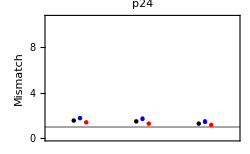
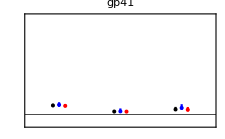
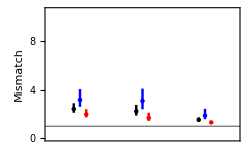
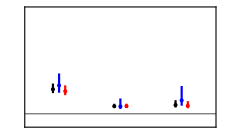
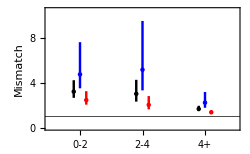
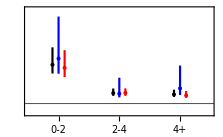
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
Column[{
Row[{ylaba,PlotFigure[patients,"gag",1,10000],PlotFigure[patients,"gp41",1,10000]}],
Row[{ylabb,PlotFigure[patients,"gag",2,10000],PlotFigure[patients,"gp41",2,10000]}],
Row[{ylabc,PlotFigure[patients,"gag",3,10000],PlotFigure[patients,"gp41",3,10000]}]}]
```